```mathematica
path = "/home/michal4/Documents/studia/uj-spe/lab02/docs/plots/";
rawData = Import[path<>"results-rlc-4-filtered.csv","CSV"];
rawData = Drop[rawData,1];
```

```mathematica
fitData = {#2,#4/#3}&@@@rawData;
R=1776;
model = NonlinearModelFit[
fitData,
{Sqrt[R^2/(R^2+(1/(1/(x 2 Pi L)-x 2 Pi c))^2)],L>0,L<0.1,c>0,c<10^-8},{L,c}, x,Method->"NMinimize"];
bestFit = model["BestFitParameters"]
valL = bestFit[[1]][[2]];
valC = bestFit[[2]][[2]];
1/(2 Pi Sqrt[valL valC])
```

{L→0.0111311,c→3.28454×10^-9}

26321.7

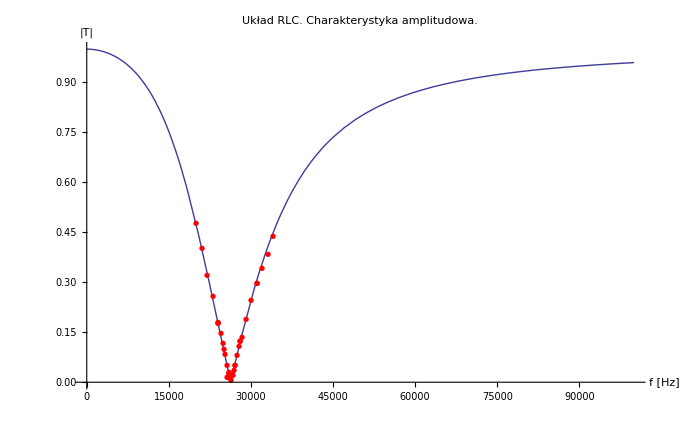

```mathematica
Show[
Plot[model[x],{x,0,100000},
PlotRange->{Automatic,{0,1}},
BaseStyle->{FontSize->16},
PlotLabel-> "Układ RLC. Charakterystyka amplitudowa.",
AxesLabel->{"f [Hz]","|T|"}],
ListPlot[fitData,PlotMarkers->{Automatic,7},PlotStyle->Red]
]
```

```mathematica
fitDataPhase={#2,-#5}&@@@rawData;
modelPhase = NonlinearModelFit[
fitDataPhase,
{ArcTan[-1/(R(1/(2 Pi x L)-2 Pi x c))]/Degree,L>0.0001,L<0.1,c>0,c<10^-8},{L,c}, x,Method->"NMinimize"];
modelPhase2[x_]:=ArcTan[-1/(R(1/(2 Pi x 10*10^-3)-2 Pi x 3.65*10^-9))]/Degree;
bestFitPhase = modelPhase["BestFitParameters"]
valLPhase = bestFitPhase[[1]][[2]];
valCPhase = bestFitPhase[[2]][[2]];
1/(2 Pi Sqrt[valLPhase valCPhase])
```

{L→0.015673,c→2.32948×10^-9}

26340.

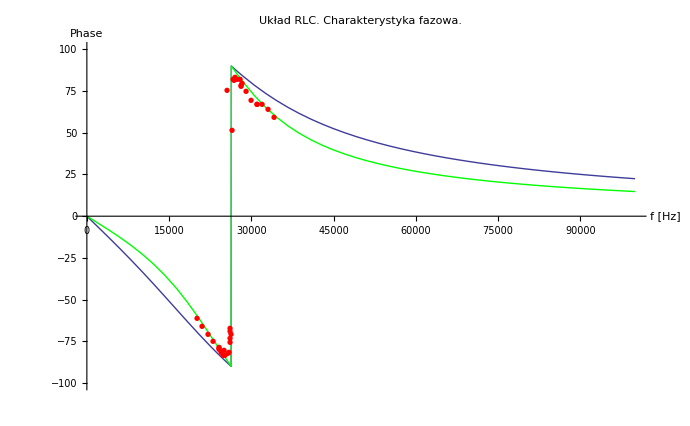

```mathematica
Show[
Plot[modelPhase[x],{x,0,100000},
PlotRange->{Automatic,{-100,100}},
BaseStyle->{FontSize->16},
PlotLabel-> "Układ RLC. Charakterystyka fazowa.",
AxesLabel->{"f [Hz]","Phase"}],
Plot[modelPhase2[x],{x,0,100000},PlotStyle->Green],
ListPlot[fitDataPhase,PlotMarkers->{Automatic,7},PlotStyle->Red]
]
```